{{s→InterpolatingFunction[…],e→InterpolatingFunction[…],i→InterpolatingFunction[…],r→InterpolatingFunction[…]}}

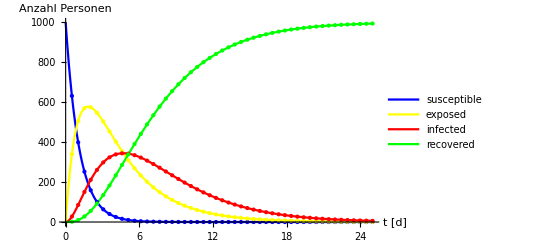

susceptile

{1.691×10^-7}

exposed

{1.691×10^-7}

infected

{5.81153}

recovered

{994.358}

```mathematica
n=1000; (*Start Population*)
endt=25; (*Ende t der Simulation*)
a=0.9;(*Infektionsrate*)
b=0.3;(*Genesungsrate*)
c=0.3;(*Übergangsrate von Exposed zu Infected*)
d=0.1;(*Übergangsrate von Susceptible zu Exposed*)
u=0.12;(*Todesrate*)


system={
differenzialS=s'[t]==-a*s[t],(*Susceptile*)
differenzialE=e'[t]== a*s[t]-c*e[t],(*Exposed*)
differenzialI=i'[t]==c*e[t]-b*i[t],(*Infective*)
differenzialR=r'[t]==b*i[t](*Recovered*)


};
anfangswerte={
s[0]==n,
e[0]==1,
i[0]==0,
r[0]==0

};
lösung=NDSolve[{system,anfangswerte},{s,e,i,r},{t,0,100}](*löse das GLS*)
lösungS=First[s/.lösung];(*erhalte erstes Element von Liste*)
lösungE=First[e/.lösung];
lösungI=First[i/.lösung];
lösungR=First[r/.lösung];


graph=
Plot[{lösungS[t],lösungE[t],lösungI[t],lösungR[t]},{t,0,endt},
PlotRange->{0,n},
PlotStyle->{Blue,Yellow,Red,Green},
PlotLegends->{"susceptible","exposed","infected","recovered"},
Mesh->Full,
AxesLabel->{"t [d]","Anzahl Personen"}
]
"susceptile"
s[endt]/.lösung
"exposed"
s[endt]/.lösung
"infected"
i[endt]/.lösung
"recovered"
r[endt]/.lösung
```

```mathematica
{{□}, {□}}
```

{{□},{□}}